2

{{y[x]→InterpolatingFunction[…][x]}}

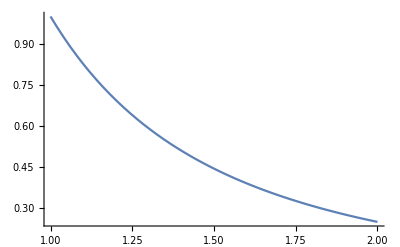

```mathematica
Clear["Global`*"]
T=2
s=NDSolve[{y''[x]==6*y[x]^2,y[1]==1,y'[1]==-2},y[x],{x,1,T}]
Plot[Evaluate[y[x]/.s],{x,1,T},PlotRange->All]
```